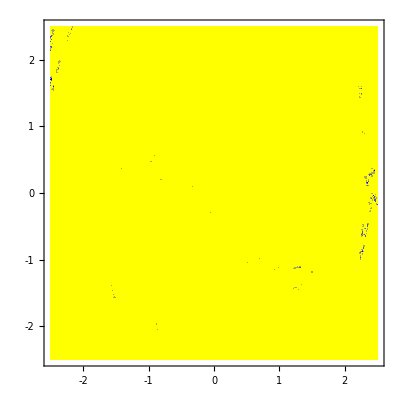

```mathematica
ClearSystemCache;

DuffingForced={x'[t]==y[t],y'[t]==x[t]-x[t]^3-0.25 y[t]+1.0* Cos[t]};

tmax=8*Pi;
AttractingWell[a_,b_]:=Sign[x[t]]/.First[NDSolve[{DuffingForced,x[0]==a,y[0]==b},{x[t],y[t]},{t,0,tmax}]]/.t->tmax;
DensityPlot[AttractingWell[a,b],{a,-2.5,2.5},{b,-2.5,2.5},PlotPoints->130,MaxRecursion->3,Mesh->False,ColorFunction->(If[# ≠ 1,Blue,Yellow] &), FrameTicks->{Range[-2,2],Range[-2,2],None,None}]
```